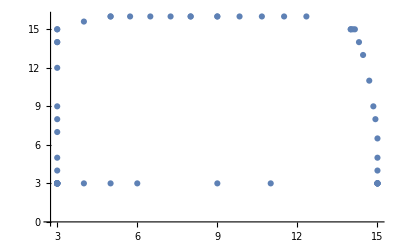

```mathematica
data = Import["D:\\Créations Persos\\Progra\\C++\\Visual Studio\\PatternRecognition\\PatternRecognition\\data.txt", "Table"];
ListPlot[data]
```

InterpolatingFunction::dmval: Input value {0.0000306429} lies outside the range of data in the interpolating function. Extrapolation will be used.

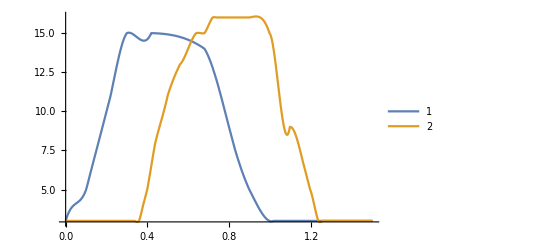

ParametricPlot::pllim: Range specification funcY[t] is not of the form {x, xmin, xmax}.

ParametricPlot[funcX[t],funcY[t],{t,0,5}]

```mathematica
dataX = Import["D:\\Créations Persos\\Progra\\C++\\Visual Studio\\PatternRecognition\\PatternRecognition\\x.txt", "Table"];
funcX = Interpolation[dataX];
dataY = Import["D:\\Créations Persos\\Progra\\C++\\Visual Studio\\PatternRecognition\\PatternRecognition\\y.txt", "Table"];
funcY = Interpolation[dataY];
Plot[{funcX[t], funcY[t]}, {t, 0, 1.5}, PlotLegends->Automatic]
```